```mathematica
SetOptions[ListLinePlot, ImageSize->800, Frame -> True, Axes->False];

PrepareData[filename_] := Block[{data, mapping, dataTmp, dataKugelkoordinaten},
data = Drop[Import["/home/nils/Projects/C/Handschuh/USB/driver/" <> filename <> ".dat", "Table"], -1];
mapping = CoordinateTransformData["Cartesian"->"Spherical", "Mapping"];
(* r, θ, ϕ *)
Quiet[data /. {x_,y_,z_} -> mapping[{x,y,z}]]
]
PlotCalibrate[data_] := ListLinePlot[{data[[All, 1,1]], data[[All, 1,2]], data[[All, 1,3]]}, PlotRange->Full, PlotLegends->{"r","θ","ϕ"}]
PlotData[data_] := ListLinePlot[{data[[All, 1]], data[[All, 2]], data[[All, 3]]}, PlotRange->Full, PlotLegends->{"r","θ","ϕ"}]
Calibrate[data_, span_] := Block[{dataGood = data/.{x_,y_,Indeterminate} -> {x,y,0}}, # - {0}~Join~Mean[dataGood[[span]]][[{2,3}]]&/@dataGood]
WordReplacement = {"Steady" -> 0, "Down" -> 1};

(* Gesture Down *)
dataGestureDown = PrepareData["gesture_down"];
dataGestureDown = Calibrate[dataGestureDown, 2;;400];
dataGestureDown2 =  PrepareData["gesture_down2"];
dataGestureDown = dataGestureDown ~Join~ Calibrate[dataGestureDown2, 2;;300];
dataPoseSteady = # -> "Steady"&/@ (dataGestureDown[[2;;400]] ~Join~ dataGestureDown[[1100;;1700]]);
dataPoseDown = # -> "Down"&/@ (dataGestureDown[[500;;950]] ~Join~ dataGestureDown[[1850;;1950]] ~Join~ dataGestureDown[[2300;;2500]]);

(* Classifier *)
classified = Classify[dataPoseSteady ~Join~ dataPoseDown];
PlotClassify[data_, classfifier_] := Show[{PlotData[data], ListLinePlot[classfifier[data] /. WordReplacement]}]
```

## Test

Data

```mathematica
(* Gesture Down Test *)
dataGestureDownTest =  PrepareData["gesture_down_test"];
dataGestureDownTest = Calibrate[dataGestureDownTest, 2;;700];
(* Gesture Up Test *)
dataGestureUpTest =  PrepareData["gesture_up_test"];
dataGestureUpTest = Calibrate[dataGestureUpTest, 2;;200];
```

Plots

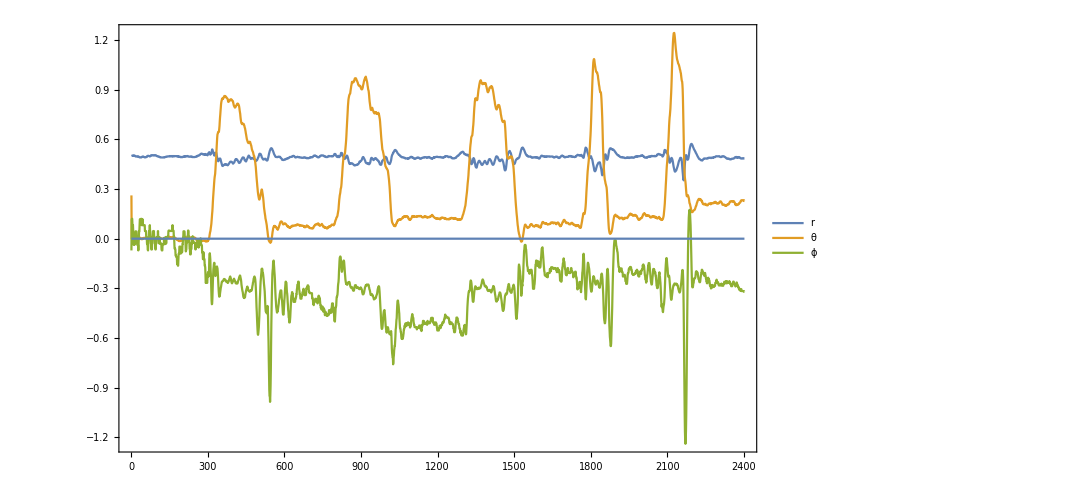

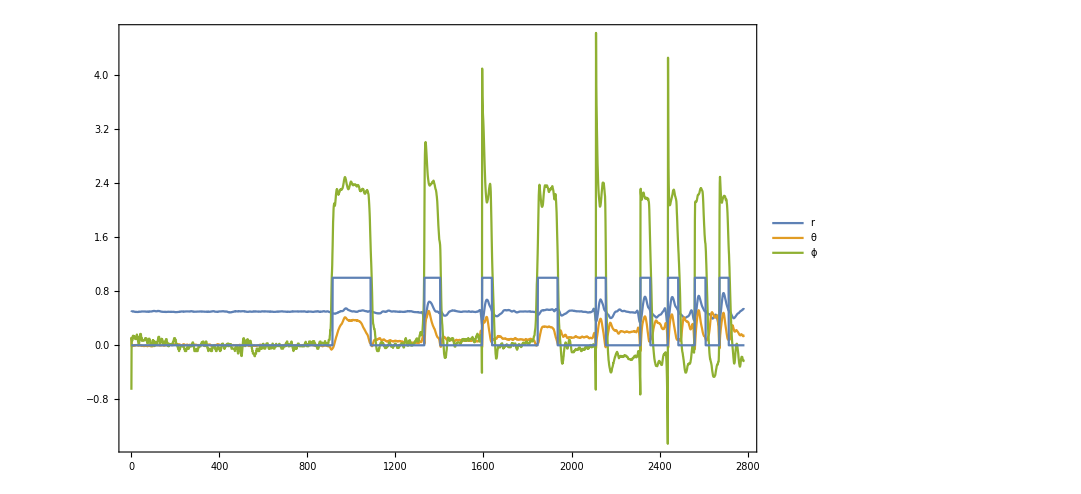

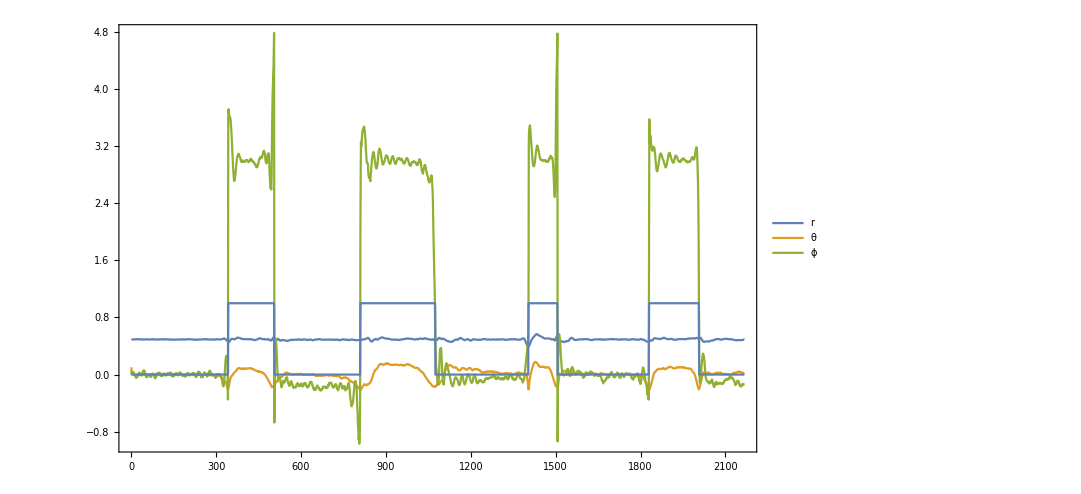

```mathematica
PlotClassify[dataGestureUpTest, classified]
PlotClassify[dataGestureDownTest, classified]
```

```mathematica
(*GetParameters[dataPiece_/;Length[dataPiece] ≠ 200] := Missing[]
GetParameters[dataPiece_/;Length[dataPiece] == 200] := Block[{
max = Flatten[MaximalBy[#, Identity, 1]& /@ {dataPiece[[All,1]], dataPiece[[All, 2]], dataPiece[[All, 3]]}], min = Flatten[MinimalBy[#, Identity, 1]& /@ {dataPiece[[All,1]], dataPiece[[All, 2]], dataPiece[[All, 3]]}]},
{
"StartValue" -> dataPiece[[1]],
"EndValue" -> dataPiece[[-1]],
"MaxValue" -> max,
"MinValue" -> min,
"Length" -> (Function[i,Length[Select[dataPiece[[All, i]], min[[i]] < # < max[[i]]&]]] /@ {1,2,3})
}]
dataClassify = Table[GetParameters[data[[i;;i+199]]] ,{i,1,900,1}];*)
```

```mathematica
(*Classifier[i_/; 539 ≤ i ≤ 600] := Flatten[{"StartValue", "EndValue", "MaxValue", "MinValue", "Length"} /. dataClassify[[i]]] -> "A"
Classifier[i_] := Flatten[{"StartValue", "EndValue", "MaxValue", "MinValue", "Length"} /. dataClassify[[i]]] -> "0"
dataClassifyClassified = Table[Classifier[i], {i,1,Length[dataClassify]}];
Classified = Classify[dataClassifyClassified];*)
```

```mathematica
(*Solution = Table[
Flatten[{"StartValue", "EndValue", "MaxValue", "MinValue", "Length"} /.GetParameters[data[[i;;i+199]]]],
{i,1,Length[data] - 200,1}];*)
```

$Aborted

```mathematica
(*GraphicsRow[Solution/. {"A" -> Graphics[{Red, Rectangle[]}], "0" -> Graphics[{Black, Rectangle[]}]}]*)
```

```mathematica
ListAnimate[Graphics3D[Arrow[{{0,0,0}, #/Norm[#]}], PlotRange->1]&/@Take[data,400]]
```

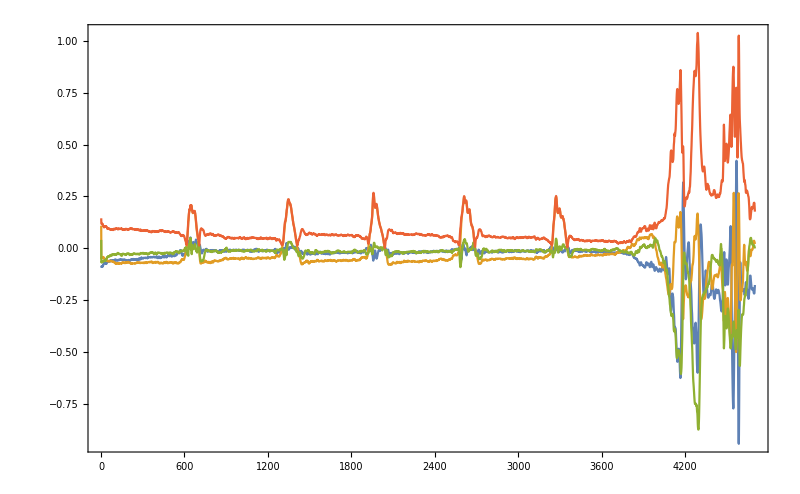

```mathematica
ListLinePlot[{data[[All, 1]], data[[All, 2]], data[[All, 3]], Norm[#]&/@data}, PlotRange->Full]
```

```mathematica
a = 1->2
```

1→2

```mathematica
a[[2]]
```

2